# Resonance and mode conversion

## 1. Global constants

```mathematica
hbar=1.0545718176461565*10^-27;
e=4.803204712570263*10^(-10);
me=9.1093837015*10^(-28);
mp=1.67262192369*10^-24;
A=1;Z=1;Ye=1;
kb=1.380649*10^(-16);
kev2erg=1.6021766339999998*10^-9;
c=29979245800.0;
σT=8*π/3*e^4/(c^4 me^2);
κT=σT/mp;
G=6.674299999999999*10^-8;
Ms=1.988409870698051*10^33;
km=10^5;
αF=e^2/(hbar c);
BQ=me^2*c^3/e/hbar;
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
```

## Temperature profile

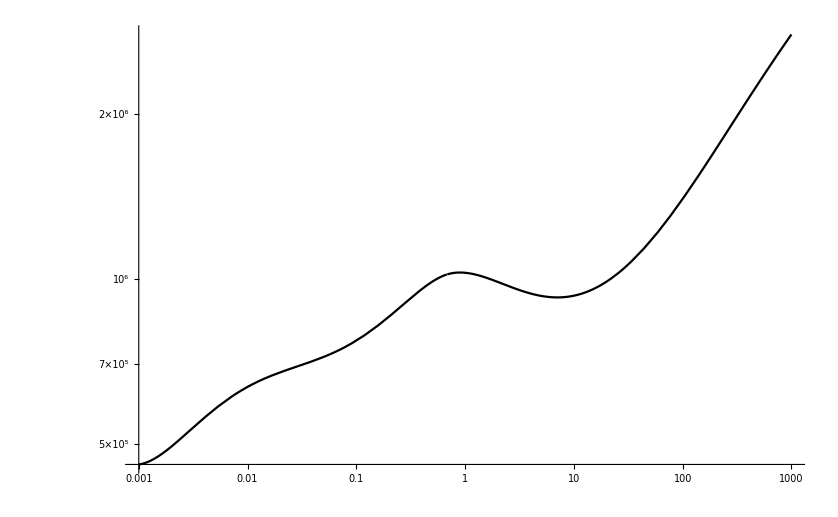

```mathematica
temperature[τ_]:=Module[{τmid,x},
τmid=0.683;
a1=0.00828;
a2= 0.0614;
a3=-0.304;
a4=0.266;
a5= -0.0719;
a6=0.00652;
b3=-0.313;
b4=-0.374;
b5=-0.162;
b6=-0.0234;
x=Log[10,τ]-Log[10,τmid];
Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}]];
LogLogPlot[temperature[τ],{τ,0.001,10^3},Background->White,PlotTheme->"Monochrome"]
```

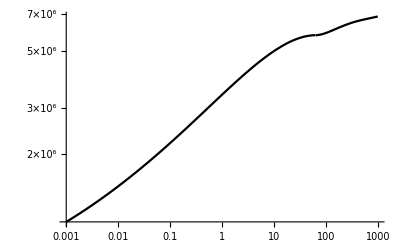

```mathematica
temperature[τ_]:=Module[{τmid,x},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}]];
LogLogPlot[temperature[τ],{τ,0.001,10^3},Background->White,PlotTheme->"Monochrome"]
```

```mathematica
temperature[3000]
```

7.54804×10^6

## opacity and density relation

```mathematica
τ2ρ[τ_]:=Module[{Mns,Rns,gns,T,sol},
T=temperature[τ];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
sol=(mp*gns*τ)/(2*kb*T*κT);
sol
]
```

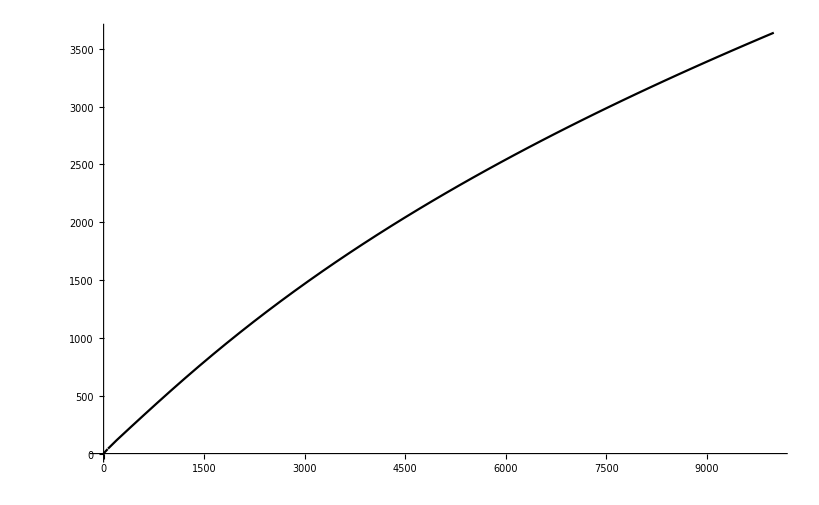

```mathematica
Plot[τ2ρ[τ],{τ,0.001,10^4},PlotTheme->"Monochrome",Background->White]
```

## Vacuum resonance

### fB

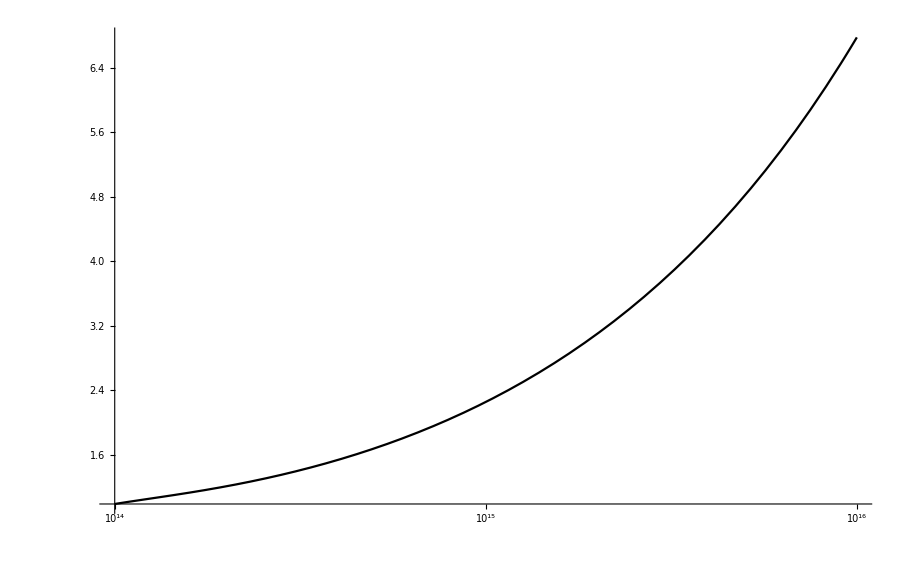

```mathematica
fB[B_]:=Module[{b,q,m,δv,sol},
b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
sol=((3*δv)/(q+m))^0.5;
sol]
LogLinearPlot[fB[B],{B,10^14,10^16},PlotTheme->"Monochrome",Background->White]
```

### resonant density

```mathematica
ρreson[Es_,B_]:=Module[{q,m,Mns,Rns,b,δv,fB,gns,ρv},
b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
ρv]
```

```mathematica
ρreson[0.35,5*10^14]
```

1.04295

### resonant optical depth

```mathematica
τreson[Es_,B_]:=Module[{q,m,ωc,Ebi,Mns,Rns,Ead,b,δv,fB,gns,ρv,τv},
b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*5*10^6))^-1}];
τv]
```

```mathematica
τreson[5,5*10^14]
```

375.212

## Decoupling density

```mathematica
decouple[Es_,B_,T_]:=Module[{ρo,ρx,ρv,b,q,m,δv,fB},
b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
ρo=0.42*(T/10^6)^(-1/4)Es^1.5(1-Exp[-Es*kev2erg/kb/T])^-0.5;
ρx=486*(T/10^6)^(-1/4)Es^0.5 B/10^14(1-Exp[-Es*kev2erg/kb/T])^-0.5;
{ρv,ρo,ρx}
]
decouple[5,5*10^14,5*10^6]
```

{212.848,3.14025,3633.71}

```mathematica
Pjump[Es_,B_,θb_]:=Module[{τv,Tv,Hρ,jump,b,q,m,δv,fB,Mns,Rns,gns,ωc,Ebi,ρv,Ead},

b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=1*10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ωc=(e B)/(me c);
Ebi=hbar*ωc*me/mp/kev2erg;
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*10^6))^-1}];
Print[τv];
Tv=temperature[τv];

Hρ=Abs[2*kb*Tv/(mp * gns *Cos[θb])];
Print[Hρ];
Ead=2.52*(fB*Tan[θb])^(2/3)*(Abs[1-(Ebi/Es)^2])^(2/3)(1/Hρ)^(1/3);
jump=Exp[-π/2(Es/Ead)^3];
N[jump]
]
Pjump[5,5*10^14,π/4]
```

375.212

6.26814

2.27888×10^-33

```mathematica
Pjump[Es_,B_,θb_]:=Module[{jump},

b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=1*10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ωc=(e B)/(me c);
Ebi=hbar*ωc*me/mp/kev2erg;
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*10^6))^-1}];
Tv=temperature[τv];

Hρ=Abs[2*kb*Tv/(mp * gns *Cos[θb])];
Ead=2.52*(fB*Tan[θb])^(2/3)*(Abs[1-(Ebi/Es)^2])^(2/3)(1/Hρ)^(1/3);
jump=Exp[-π/2(Es/Ead)^3];
N[jump]
]
Pjump[0.65,10^14,π/4]
```

1.38897×10^-9

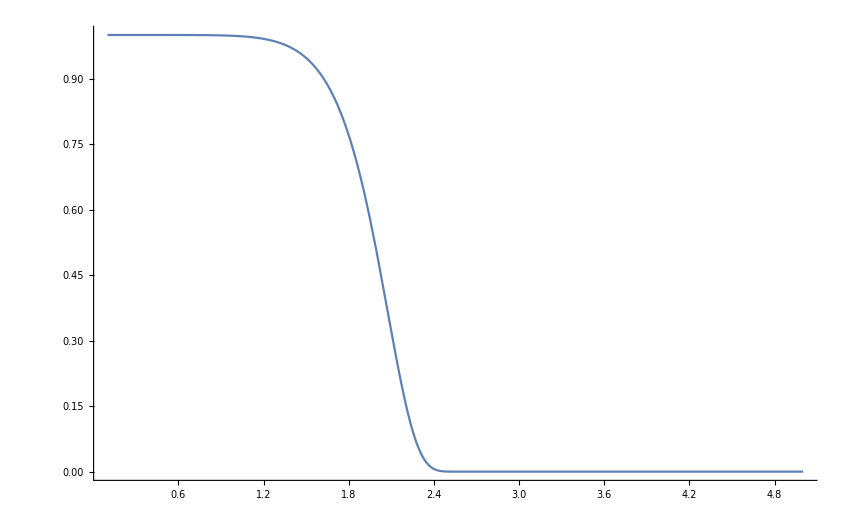

```mathematica
Plot[Pjump[x,5*10^14,π/4],{x,0.1,5},PlotRange->All]
```

```mathematica
N[Exp[-π/2 0.275]]
```

0.64923